```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[7],Join[Table[{i,i-1},{i,Range[2,7,1]}],Table[{i,i+1},{i,Range[1,7,1]}]]->-t]
```

```mathematica
T[t_]:=T[t]=t*IdentityMatrix[7]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,1,0]],A:=Inverse[β[ω,δ,1,0]],T:=T[1]},Do[J=Inverse[IdentityMatrix[7]-A.T.J.T].A,25000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T[1].LEFT[ω,δ,t,ϵ].T[1]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T[1].LEFT[ω,δ,t,ϵ].T[1]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,δ,1,0].T[1].SR[ω,δ,1,0].T[1]].SL[ω,δ,1,0]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,1,0].T[1].SL[ω,δ,1,0].T[1]].SR[ω,δ,1,0]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,1,0].T[1].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T[1].grr[ω,δ,t,ϵ].T[1]-T[1].GNON[ω,δ,t,ϵ].T[1].GNON[ω,δ,t,ϵ]]
```

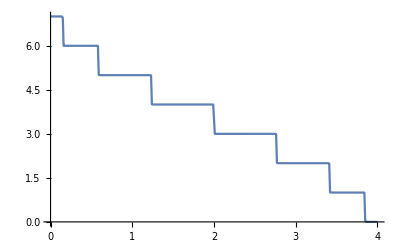
{373.685,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[0,4,0.01]}]]]
```

```mathematica
imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{1,1}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{2,2}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{3,3}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{4,4}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{5,5}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{6,6}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{7,7}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
set[ω_,δ_,t_,ϵ_,ϵ1_,num_]:=(*set[ω,δ,t,ϵ,ϵ1,num]=*)RandomChoice[Join[Table[RandomChoice[{imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp3[ω,δ,t,ϵ,ϵ1],imp4[ω,δ,t,ϵ,ϵ1],imp5[ω,δ,t,ϵ,ϵ1],imp6[ω,δ,t,ϵ,ϵ1],imp7[ω,δ,t,ϵ,ϵ1]}],num],Table[imp7[ω,δ,t,ϵ,0],100-num]],100]
```

```mathematica
Clear[a1,a3,a4,a3,a5,a6,a7,a8,set,tr1]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_,num_]:=Module[{gg=g[ω,δ,t,ϵ],x=T[1],J=SL[ω,δ,t,ϵ]},
sl1= Module[{},Do[J=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].ConjugateTranspose[x].J.x].imp7[ω,δ,t,ϵ,ϵ1],{ζ,1}];J=J];Il1:=Inverse[IdentityMatrix[7]-sl1.x.SR[ω,δ,t,ϵ].x].sl1;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].x.sl1.x].SR[ω,δ,t,ϵ];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,t,ϵ].x.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.x.grr1.x-x.GNON1.x.GNON1]]]
```

```mathematica
Table[{ω,tr1[ω,0.001,1,0,1,100]},{ω,Range[0,4,0.01]}]
```

{{0.,6.58423},{0.01,6.58372},{0.02,6.5821},{0.03,6.57928},{0.04,6.57513},{0.05,6.5694},{0.06,6.56174},{0.07,6.55159},{0.08,6.53806},{0.09,6.51972},{0.1,6.49402},{0.11,6.45608},{0.12,6.39512},{0.13,6.28192},{0.14,5.99777},{0.15,3.74923},{0.16,4.12935},{0.17,5.06904},{0.18,5.30828},{0.19,5.41522},{0.2,5.4751},{0.21,5.51296},{0.22,5.53875},{0.23,5.5572},{0.24,5.57082},{0.25,5.58108},{0.26,5.58888},{0.27,5.59481},{0.28,5.59927},{0.29,5.60254},{0.3,5.60479},{0.31,5.60618},{0.32,5.60679},{0.33,5.60669},{0.34,5.60594},{0.35,5.60454},{0.36,5.60251},{0.37,5.59984},{0.38,5.59651},{0.39,5.59248},{0.4,5.5877},{0.41,5.58209},{0.42,5.57556},{0.43,5.56797},{0.44,5.55917},{0.45,5.54893},{0.46,5.53698},{0.47,5.52294},{0.48,5.50628},{0.49,5.48629},{0.5,5.46194},{0.51,5.43169},{0.52,5.39316},{0.53,5.34242},{0.54,5.27245},{0.55,5.1694},{0.56,5.00115},{0.57,4.67041},{0.58,3.63521},{0.59,12.7492},{0.6,0.648117},{0.61,2.83821},{0.62,3.55855},{0.63,3.90113},{0.64,4.09748},{0.65,4.22333},{0.66,4.3102},{0.67,4.37338},{0.68,4.42114},{0.69,4.45834},{0.7,4.48798},{0.71,4.51205},{0.72,4.53187},{0.73,4.54839},{0.74,4.56228},{0.75,4.57405},{0.76,4.58408},{0.77,4.59265},{0.78,4.59998},{0.79,4.60626},{0.8,4.61163},{0.81,4.61619},{0.82,4.62005},{0.83,4.62326},{0.84,4.6259},{0.85,4.62802},{0.86,4.62964},{0.87,4.6308},{0.88,4.63154},{0.89,4.63185},{0.9,4.63177},{0.91,4.6313},{0.92,4.63045},{0.93,4.62921},{0.94,4.62758},{0.95,4.62555},{0.96,4.62312},{0.97,4.62026},{0.98,4.61696},{0.99,4.61318},{1.,4.6089},{1.01,4.60406},{1.02,4.59863},{1.03,4.59254},{1.04,4.58572},{1.05,4.57808},{1.06,4.56951},{1.07,4.55988},{1.08,4.54902},{1.09,4.53672},{1.1,4.52273},{1.11,4.5067},{1.12,4.48819},{1.13,4.46662},{1.14,4.44119},{1.15,4.41076},{1.16,4.37371},{1.17,4.32759},{1.18,4.26846},{1.19,4.18966},{1.2,4.07872},{1.21,3.90887},{1.22,3.60763},{1.23,2.83941},{1.24,5.8521},{1.25,8.11662},{1.26,1.67821},{1.27,0.779987},{1.28,1.84024},{1.29,2.39398},{1.3,2.72378},{1.31,2.93871},{1.32,3.08812},{1.33,3.19708},{1.34,3.27954},{1.35,3.34378},{1.36,3.39501},{1.37,3.43665},{1.38,3.47105},{1.39,3.49983},{1.4,3.52419},{1.41,3.545},{1.42,3.56292},{1.43,3.57846},{1.44,3.592},{1.45,3.60385},{1.46,3.61427},{1.47,3.62346},{1.48,3.63157},{1.49,3.63873},{1.5,3.64507},{1.51,3.65066},{1.52,3.65559},{1.53,3.65993},{1.54,3.66371},{1.55,3.667},{1.56,3.66982},{1.57,3.67221},{1.58,3.6742},{1.59,3.67582},{1.6,3.67706},{1.61,3.67797},{1.62,3.67854},{1.63,3.67878},{1.64,3.6787},{1.65,3.67831},{1.66,3.6776},{1.67,3.67657},{1.68,3.67522},{1.69,3.67355},{1.7,3.67153},{1.71,3.66917},{1.72,3.66644},{1.73,3.66332},{1.74,3.6598},{1.75,3.65583},{1.76,3.6514},{1.77,3.64645},{1.78,3.64095},{1.79,3.63483},{1.8,3.62804},{1.81,3.62048},{1.82,3.61206},{1.83,3.60267},{1.84,3.59216},{1.85,3.58037},{1.86,3.56706},{1.87,3.55197},{1.88,3.53475},{1.89,3.51493},{1.9,3.49191},{1.91,3.46487},{1.92,3.43267},{1.93,3.39364},{1.94,3.34533},{1.95,3.28383},{1.96,3.20256},{1.97,3.08931},{1.98,2.91792},{1.99,2.61531},{2.,1.57486},{2.01,4.17062},{2.02,11.4195},{2.03,5.66176},{2.04,1.52105},{2.05,0.240659},{2.06,1.09761},{2.07,1.57641},{2.08,1.87267},{2.09,2.07013},{2.1,2.20925},{2.11,2.31154},{2.12,2.38932},{2.13,2.45007},{2.14,2.49858},{2.15,2.53804},{2.16,2.57062},{2.17,2.59787},{2.18,2.62092},{2.19,2.6406},{2.2,2.65752},{2.21,2.67219},{2.22,2.68497},{2.23,2.69615},{2.24,2.70598},{2.25,2.71465},{2.26,2.7223},{2.27,2.72907},{2.28,2.73506},{2.29,2.74036},{2.3,2.74504},{2.31,2.74916},{2.32,2.75278},{2.33,2.75594},{2.34,2.75867},{2.35,2.761},{2.36,2.76296},{2.37,2.76458},{2.38,2.76586},{2.39,2.76682},{2.4,2.76748},{2.41,2.76784},{2.42,2.7679},{2.43,2.76768},{2.44,2.76716},{2.45,2.76634},{2.46,2.76523},{2.47,2.76382},{2.48,2.76208},{2.49,2.76002},{2.5,2.75761},{2.51,2.75482},{2.52,2.75165},{2.53,2.74805},{2.54,2.74399},{2.55,2.73942},{2.56,2.73429},{2.57,2.72854},{2.58,2.7221},{2.59,2.71486},{2.6,2.70672},{2.61,2.69754},{2.62,2.68715},{2.63,2.67533},{2.64,2.6618},{2.65,2.64621},{2.66,2.6281},{2.67,2.60682},{2.68,2.58152},{2.69,2.55096},{2.7,2.51334},{2.71,2.46586},{2.72,2.40403},{2.73,2.31991},{2.74,2.19806},{2.75,2.00278},{2.76,1.6163},{2.77,0.576643},{2.78,13.8674},{2.79,12.9007},{2.8,2.48488},{2.81,0.116525},{2.82,0.725862},{2.83,1.1231},{2.84,1.34433},{2.85,1.48154},{2.86,1.57324},{2.87,1.63798},{2.88,1.68562},{2.89,1.72183},{2.9,1.75009},{2.91,1.7726},{2.92,1.79085},{2.93,1.80586},{2.94,1.81836},{2.95,1.82887},{2.96,1.83777},{2.97,1.84537},{2.98,1.85189},{2.99,1.8575},{3.,1.86234},{3.01,1.86652},{3.02,1.87014},{3.03,1.87325},{3.04,1.87592},{3.05,1.87819},{3.06,1.88011},{3.07,1.8817},{3.08,1.88298},{3.09,1.88398},{3.1,1.88472},{3.11,1.88519},{3.12,1.88542},{3.13,1.8854},{3.14,1.88513},{3.15,1.88462},{3.16,1.88385},{3.17,1.88283},{3.18,1.88152},{3.19,1.87992},{3.2,1.878},{3.21,1.87574},{3.22,1.8731},{3.23,1.87003},{3.24,1.86648},{3.25,1.86237},{3.26,1.85762},{3.27,1.85212},{3.28,1.84572},{3.29,1.83823},{3.3,1.8294},{3.31,1.81889},{3.32,1.80623},{3.33,1.79073},{3.34,1.77139},{3.35,1.74666},{3.36,1.71397},{3.37,1.66884},{3.38,1.60253},{3.39,1.49536},{3.4,1.29126},{3.41,0.722663},{3.42,20.4012},{3.43,3.01802},{3.44,0.015751},{3.45,0.528669},{3.46,0.712117},{3.47,0.800513},{3.48,0.850599},{3.49,0.882023},{3.5,0.903164},{3.51,0.918124},{3.52,0.929119},{3.53,0.937439},{3.54,0.94388},{3.55,0.948954},{3.56,0.953007},{3.57,0.956274},{3.58,0.958926},{3.59,0.961083},{3.6,0.962835},{3.61,0.964248},{3.62,0.965371},{3.63,0.966242},{3.64,0.966885},{3.65,0.96732},{3.66,0.967558},{3.67,0.967605},{3.68,0.967459},{3.69,0.967113},{3.7,0.966554},{3.71,0.965758},{3.72,0.964691},{3.73,0.963306},{3.74,0.961531},{3.75,0.959267},{3.76,0.956366},{3.77,0.952603},{3.78,0.947619},{3.79,0.940812},{3.8,0.931086},{3.81,0.916216},{3.82,0.890889},{3.83,0.838453},{3.84,0.66456},{3.85,3.41507},{3.86,0.222143},{3.87,0.0910916},{3.88,0.0523456},{3.89,0.0348034},{3.9,0.0251207},{3.91,0.0191179},{3.92,0.0150998},{3.93,0.0122592},{3.94,0.010167},{3.95,0.00857602},{3.96,0.00733491},{3.97,0.00634618},{3.98,0.00554458},{3.99,0.00488494},{4.,0.00433514}}

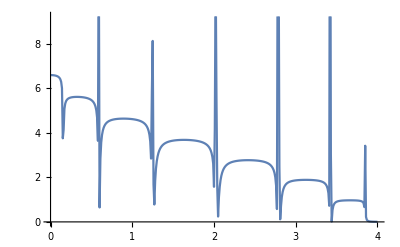

```mathematica
ListPlot[%34,Joined->True]
```

```mathematica
Table[tr1[.2,0.001,1,0,0.5,100],1000]
```

{20.5544,81.11,9.62119,87.2821,24.2525,15.1279,23.7165,1415.04,127.968,8.50753,63.2576,29.6831,89.028,30.6271,57.707,492.808,122.999,1939.79,31.8403,2743.48,181.595,512.083,9.17805,19.998,36.2667,41.0222,60.7421,26.7312,410.471,398.101,33.9074,199.209,55.485,185.218,59.9069,318.443,169.157,34.3213,63.8231,95.2429,77.4319,9.24445,161.556,85.2189,41.2932,4.48351,8.1453,122.824,45.186,252.28,9.32334,389.032,56.5051,65.1234,308.995,108.542,2.82876,39.6549,26.3566,48.056,92.6694,32.5744,141.259,170.475,300.379,13.3677,21.6104,143.66,91.7302,126.325,2449.34,163.858,3094.43,37.5123,92.6656,612.847,19.4875,1002.33,75.4184,78.0522,44.6889,16.8904,9.67195,93.0356,9.5952,11.9769,29.0511,146.883,107.381,138.65,20.5539,170.049,164.953,27.8954,39.7518,7.19195,1033.19,145.233,29.3684,9.02538,193.382,142.16,16.4773,73.5362,8557.42,120.922,145.734,30.9776,22.2811,121.021,9.16258,10.7191,29.7819,609.443,25.9885,152.947,19.06,3581.34,72.0102,1990.01,878.128,19.5599,19.0709,15.5135,64.1696,16.6027,92.146,28.5204,453.679,115.457,7.97718,1300.36,71.8037,9.98745,13.6538,9.31413,61.3302,179.727,501.547,1105.13,47.2777,114.691,28.6269,52.634,13.8108,111.867,10.1639,1590.82,676.713,121.651,162.494,34.161,158.087,338.837,926.654,219.71,66.7875,11.0418,201.919,15.4239,3127.7,53.759,56.0401,168.134,44.7246,34.0188,49.91,22.4528,46.9266,36.5882,27.2272,69.2034,42.9402,180.898,348.806,17.899,80.2467,64.2059,104.934,11.1123,101.865,57.8225,97.0916,569.103,76.4911,7.31537,194.871,154.396,196.898,23.3045,89.849,65.7706,85.949,268.329,275.671,132.838,34.5613,15464.3,32.8641,56.4355,20.5059,767.892,19.7871,295.307,98.5238,297.155,723.393,7.00305,12.8614,10.2709,64.2555,124.952,916.604,2965.51,59.149,163.361,1045.4,521.082,475.417,309.305,215.328,267.935,43.3681,17.0865,75.5925,78.0437,232.994,70.6254,80.2984,200.517,24.1413,43.7019,289.191,323.46,36.9781,54.8966,508.949,50.9506,233.808,284.124,72.0479,145.628,119.936,392.827,28.9242,12.8707,101.431,300.09,90.614,60.2014,585.225,77.0866,70.6677,28.1495,44.1743,24.0501,41.8895,23.5333,552.656,8671.79,69.5191,130.499,104.415,448.832,80.7871,39.1863,54.6336,738.972,38.7294,7.62342,71.956,226.175,672.309,29.5289,33.3675,569.591,62.3505,128.689,169.25,214.142,17.166,329.907,222.748,624.138,34.9528,24.9167,35.8152,20.282,1687.54,70.8723,56.0879,169.89,39.2852,791.491,28.7942,165.967,294.303,14839.2,35.8785,10.7236,67.8101,16.6501,46.996,164.508,12.2444,390.104,252.161,88.8227,45.2824,48.619,91.8263,65.2397,25.8954,429.777,77.5319,82.1488,153.615,51.0296,42.5685,310.872,12.9465,54.5851,86.3122,47.4346,57.5736,283.781,168.005,109.319,58.4701,18.1637,94.6069,10.5671,191.599,215.132,22.4114,649.35,475.261,86.3346,239.186,2691.21,494.461,13.2196,5.31462,50.4299,10.0572,32.4322,101.327,20.8828,24.8839,183.936,123.874,133.683,10.0223,64.329,55.9802,137.365,199.567,14.5112,378.889,465.973,67.8716,31.0622,2992.41,1362.28,34.3317,108.44,12.5006,108.62,19.2409,14.5003,136.301,21.1155,295.221,187.32,18.0524,4546.61,132.323,48.0031,267.001,94.6015,130.959,140.988,6.36643,13.3924,252.373,42.7481,35.9066,7.84463,42.1305,45.3608,178.108,10405.8,4.67945,221.946,205.828,23.6743,178.188,55.337,6769.16,24.1976,81.8047,223.057,38.7062,43.2353,40.9806,312.89,395.419,75.375,172.665,605.727,27.9267,339.95,945.352,68.9754,65.4505,99.5201,106.157,539.845,23.6429,49.6344,2.61834,8.38742,23.5735,100.47,169.012,225.359,51.5111,14.1237,210.084,37.0461,352.536,118.974,70.0526,194.85,97.0906,297.148,206.478,22.5916,626.281,38.6895,179.451,11.1588,98.0643,462.222,162.676,32.217,40.44,10.567,45.2976,65.9235,51.3153,283.184,64.367,20.834,57.3374,74.4417,174.516,89.0875,41.0401,38.9497,203.961,459.765,33.6869,116.813,168.564,108.841,58.826,418.573,67.5061,61.8378,761.063,24.7747,90.4096,281.027,76.4714,24.7338,498.41,40.5262,188.35,543.65,117.597,89.7986,8.06582,11.415,30.6181,35.5293,2393.14,13.9183,25.0559,161.488,32.9534,11.5712,116.244,835.003,34.1615,69.1658,32.759,176.933,28.1332,37.5719,57.8737,70785.2,4.66257,65.7727,24.9579,23.3203,77.6783,43.1863,345.09,12.8471,96.3024,117.56,21.5811,34.0938,1422.77,192.75,55.6907,47.3466,93.7585,59.3939,47.6202,23.6579,90.4659,456.974,197.154,53.9011,410.635,24.5171,42.4585,77.4537,80.2243,16.3129,67.7138,503.398,1635.63,107.564,40.8135,240.116,29.9135,16.6362,51.5671,431.928,32.9369,688.002,284.449,90.0653,104.714,23.996,65.8759,1131.79,25.8297,110.094,19.3647,12.521,127.542,269.642,27.1535,28.4335,60.5003,56.4587,422.212,30.6195,325.192,76.9076,108.54,988.671,61.0263,181.818,210.944,25.7878,32.5346,175.497,33.4959,42.3942,130.341,143.588,35.8872,67.9291,38.1508,3.06715,185.615,6.55274,202.109,54.3894,31.3224,121.284,168.491,8.18857,49.351,1120.97,294.169,254.551,38.6751,75.228,55.4664,16.3182,19.1022,914.614,16.616,13.563,252.273,134.612,82.4106,546.167,3.57286,47.1164,25.622,111.514,41.8139,62.4821,54.3417,62.9693,1383.93,568.503,372.586,72.5607,22.6122,44.5435,96.6645,274.691,77.1469,162.836,33.5055,2099.46,162.903,47.2927,174.074,278.711,307.626,21.2977,230.379,83.741,225.573,227.539,27.3388,151.352,9432.95,26.1029,170.248,103.481,68.35,22.6237,193.003,52.2148,9.30904,30.8669,42.4606,768.913,91.9102,26.5146,69.8102,7173.6,157.174,107.645,11.4072,53.9235,21.3879,14.7246,16.8405,1339.25,36.6667,265.207,112.78,32.8603,315.392,2528.68,17.5886,59.9211,7.98616,122.379,24.7501,4.65872,19.6075,29.7411,16.8552,181.816,8.41744,48.4744,1679.19,64.1049,10946.3,8.80624,147.222,59.0771,224.821,58.5072,125.082,124.49,160.352,66.0627,26.9699,23.5719,180.518,31.3651,2232.39,55.1953,55.2491,71.5969,32.9082,46.352,588.15,81.032,43.387,138.899,311.416,67.0332,59.4844,12003.2,16.4847,212.829,43.7301,54.1706,145.522,10.3256,10.7248,16.3783,109.323,68.6746,130.771,284.127,56.6297,45.5969,70.8094,53.7689,173.492,130.339,217.611,22.3398,6.87593,58.2343,22.3586,30.18,102.772,127.4,348.045,56.4661,120.139,51.4305,35.6558,34.5326,47.8856,226.869,179.079,265.113,197.646,310.427,57.8557,14.6849,24.5458,750.005,10.5645,26.8562,18.682,395.087,385.835,126.672,30.5175,25.6477,167.403,16.1076,97.0409,494.371,284.303,39.2289,293.388,89.4625,31.6382,208.936,67.31,143.309,1196.16,336.859,35.119,0.541631,11.1331,22.175,193.745,22.9582,176.29,26.884,22.3558,99.3642,11.7986,33.1069,66.0491,45.6911,47.1431,42.7155,583.319,27.9061,2518.05,90.9986,110.209,37.3991,25.2952,368.803,384.097,343.7,25.5477,160.466,76.4671,86.8638,24.1284,33.8323,522.221,27.1902,89.5296,1586.77,223.693,60.9528,105.737,17.9297,3662.15,64.0877,19616.2,1202.34,24.6137,149.857,75.3237,7.1244,43.7728,26.7054,45.6165,209.707,116.108,48.0745,5.59116,63.028,22.3095,67.9319,40.1883,169.14,75.1623,22.9765,29.4913,148.534,20.7319,28.2603,79.3847,82.1544,154.242,1191.58,20.5281,9.51503,36.0013,74.1513,185.456,43.153,16.045,344.648,72.2267,49.2994,841.236,6.8321,30.2105,117.665,107.283,246.497,35.0531,13.0953,48.8457,47.297,326.541,58.658,754.419,39.0714,155.404,112.327,251.753,56.7507,31.8323,492.118,27.7601,399.779,80.3366,87.545,37.7456,60.0288,7.97688,58.976,9.91539,136.647,195.237,112.349,369.478,1191.97,25.4647,51.0085,227.145,1753.72,115.289,69.1689,48.8641,25.0579,14.1668,18.5969,10.247,149.391,150.067,24.8403,205.548,34.5328,156.521,145.006,45.3088,182.945,48.4349,728.783,20.2823,21.6123,36.8239,76.3022,27.6289,21.6761,40.6214,631.812,478.142,435.188,139.547,557.806,88.005,189.993,22.4676,1023.24,37.8108,89.3987,13.8297,7.34563,77.0921,18.5229,48.7956,66.0857,42.5856,84.2482,105.102,20.0102,285.05,164.295,38.6395,324.605,55.5226,40676.3,13.2512,34.2004,730.904,402.709,206.771,110.135,203.393,18.0828,103.026,90.0174,202.239,29.1577,39.9604,582.979,11.244,4654.21,41.2691,231.854,17.4631,1486.15,263.18,11.0267,29.2631,138.509,113.054,38.9714,152.193,24.0077,119.124,135.414,253.477,53.4529,225.147,607.578,19.0318,35.9614,480.514,151.902,12.2818,13.4117,178.938,71.8285,252.529,60.4558,59.5902,103.215,31.4083,11.6555,547.443,30.4205,41.7834,112.212,125.876,16.733,3169.45,51.8598,18.3393,26.1038}

```mathematica
Mean[%28]
```

446.079

```mathematica
Mean[%26]
```

314789.

```mathematica
ListLinePlot[Table[tr1[ω,0.001,1,0,0.5],{ω,Range[0,4,0.01]}]]
```

$Aborted

```mathematica
Table[tr1[0,0.0001,1,0,0.5],1000]
```

```mathematica
tr10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{T=t*IdentityMatrix[7]},
sl=Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[7]-imp[ω,δ,t,ϵ,ϵ1].T.J.T].imp[ω,δ,t,ϵ,ϵ1],10]; J=J];
Il1:=Inverse[IdentityMatrix[7]-sl.T.SR[ω,0.001,1,0].T].sl;Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,1,0].T.sl.T].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].T.Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]
```

```mathematica
tr10[0,0.001,1,0,1]
```

2916.23

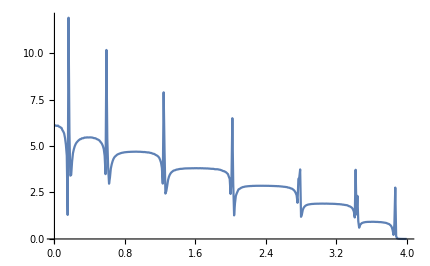

```mathematica
ListLinePlot[Table[{ωean[Table[tr10[ω,0.001,1,0,1][[1,1]],1000]]},{ω,Range[0,4,0.01]}]]
```

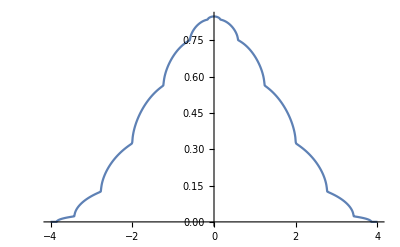

```mathematica
ListLinePlot[Table[{ω,-Im[L[ω,0.001,1,0,0][[1,1]]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
tr10[ω_,δ_,t_,ϵ_,ϵ1_,N_]:=Module[{imp=g[ω,δ,t,ϵ],T=t*IdentityMatrix[7],gg=imp[ω,δ,t,ϵ,ϵ1],X=RandomInteger[{0,2}]},sl=Module[{},leftlead=Module[{J=SL[ω,0.001,1,0]},sl11=Module[{},Do[J=Inverse[IdentityMatrix[7]-imp.T.J.T].imp,X];J=J];Do[J=Inverse[IdentityMatrix[7]-gg.T.sl11.T].gg,N]; J=J]; leftlead];
Il1:=Inverse[IdentityMatrix[7]-sl.T.SR[ω,0.001,1,0].T].sl;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,1,0].T.sl.T].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].T.Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
{{Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]],X}}]
```

```mathematica
Table[Mean[Table[tr10[0,0.001,1,0,01,100][[1,1]],Y]],{Y,Range[1000,2000,100]}]
```

```mathematica
Timing[Mean[Table[tr10[0,0.001,1,0,0.50,100][[1,1]],2500]]]
```

{6.32059,6.67853}

```mathematica
Timing[Mean[Table[tr10[0,0.001,1,0,01,100][[1,1]],3000]]]
```

{11.9552,5.8723}

```mathematica
Table[{ωean[Table[tr10[ω,0.001,1,0,1,30][[1,1]],1200]]},{ω,Range[0,4,0.01]}]
```

{{0.,5.95859},{0.01,6.29688},{0.02,6.70264},{0.03,6.6497},{0.04,6.55525},{0.05,6.26136},{0.06,6.20256},{0.07,6.06764},{0.08,5.98836},{0.09,5.48604},{0.1,5.49098},{0.11,5.11566},{0.12,4.0398},{0.13,4.47545},{0.14,3.8771},{0.15,5.31315},{0.16,5.20305},{0.17,4.84957},{0.18,4.71029},{0.19,3.72559},{0.2,4.46351},{0.21,2.89761},{0.22,1.91966},{0.23,2.876},{0.24,3.04749},{0.25,2.60784},{0.26,2.69023},{0.27,3.3509},{0.28,2.97304},{0.29,3.06373},{0.3,3.18655},{0.31,3.44434},{0.32,3.59222},{0.33,3.9027},{0.34,3.81421},{0.35,3.6739},{0.36,3.58637},{0.37,3.54292},{0.38,3.59134},{0.39,3.60061},{0.4,3.46671},{0.41,3.69295},{0.42,3.4958},{0.43,3.6089},{0.44,3.90424},{0.45,3.43336},{0.46,3.22385},{0.47,3.4733},{0.48,3.16591},{0.49,2.87966},{0.5,2.82524},{0.51,3.11254},{0.52,3.5592},{0.53,3.1543},{0.54,2.82283},{0.55,2.90894},{0.56,3.02504},{0.57,2.92801},{0.58,2.38349},{0.59,5.56815},{0.6,5.3578},{0.61,3.44629},{0.62,2.67822},{0.63,2.94226},{0.64,2.45582},{0.65,1.87968},{0.66,1.83638},{0.67,2.13984},{0.68,2.35253},{0.69,2.65639},{0.7,2.88885},{0.71,3.23053},{0.72,2.56283},{0.73,2.67886},{0.74,2.81451},{0.75,2.53685},{0.76,3.1855},{0.77,3.18699},{0.78,3.15037},{0.79,3.31827},{0.8,3.39936},{0.81,3.39508},{0.82,3.39374},{0.83,3.62702},{0.84,3.68799},{0.85,3.65287},{0.86,3.57612},{0.87,3.54668},{0.88,3.73047},{0.89,3.65181},{0.9,3.48897},{0.91,3.14487},{0.92,3.12731},{0.93,3.23176},{0.94,3.37863},{0.95,3.36576},{0.96,3.22201},{0.97,3.19628},{0.98,3.15714},{0.99,3.06711},{1.,3.23946},{1.01,3.3825},{1.02,3.35776},{1.03,3.3671},{1.04,3.34216},{1.05,3.48887},{1.06,3.5466},{1.07,3.4732},{1.08,3.39997},{1.09,3.30945},{1.1,2.90616},{1.11,2.93719},{1.12,2.73331},{1.13,2.70351},{1.14,2.65119},{1.15,2.73418},{1.16,2.85821},{1.17,2.83047},{1.18,2.75557},{1.19,2.84621},{1.2,2.86087},{1.21,3.06469},{1.22,3.4287},{1.23,4.33348},{1.24,3.97824},{1.25,3.91724},{1.26,4.54597},{1.27,3.20129},{1.28,3.47477},{1.29,3.11099},{1.3,3.2089},{1.31,2.75788},{1.32,2.21376},{1.33,2.31026},{1.34,2.53013},{1.35,2.07802},{1.36,2.57045},{1.37,2.62395},{1.38,2.52063},{1.39,2.35624},{1.4,2.37485},{1.41,2.46808},{1.42,2.55014},{1.43,2.41194},{1.44,2.54497},{1.45,2.53662},{1.46,2.64397},{1.47,2.76451},{1.48,2.9487},{1.49,3.02762},{1.5,3.06012},{1.51,3.11872},{1.52,3.19668},{1.53,3.21695},{1.54,3.27707},{1.55,3.31914},{1.56,3.25152},{1.57,3.32226},{1.58,3.43568},{1.59,3.4091},{1.6,3.33477},{1.61,3.34657},{1.62,3.35008},{1.63,3.04058},{1.64,2.83966},{1.65,2.79666},{1.66,2.81919},{1.67,2.82002},{1.68,2.79982},{1.69,2.78022},{1.7,2.85361},{1.71,2.73998},{1.72,2.73826},{1.73,2.72814},{1.74,2.7037},{1.75,2.83377},{1.76,2.71962},{1.77,2.68806},{1.78,2.51079},{1.79,2.68459},{1.8,2.64426},{1.81,2.59686},{1.82,2.71675},{1.83,2.80329},{1.84,2.70447},{1.85,2.76847},{1.86,2.731},{1.87,2.78008},{1.88,2.78036},{1.89,2.76347},{1.9,2.71952},{1.91,2.90557},{1.92,2.87471},{1.93,2.88992},{1.94,2.87352},{1.95,2.91259},{1.96,2.89392},{1.97,2.87784},{1.98,2.86617},{1.99,2.83296},{2.,2.35915},{2.01,2.23761},{2.02,2.31192},{2.03,1.93418},{2.04,1.96566},{2.05,2.09758},{2.06,2.42639},{2.07,2.10969},{2.08,2.47304},{2.09,1.62987},{2.1,2.04761},{2.11,1.67544},{2.12,1.82676},{2.13,1.89208},{2.14,1.81029},{2.15,1.94837},{2.16,2.00241},{2.17,2.19291},{2.18,2.06697},{2.19,2.20483},{2.2,2.31612},{2.21,2.39371},{2.22,2.32784},{2.23,2.43004},{2.24,2.61539},{2.25,2.42276},{2.26,2.18179},{2.27,2.16262},{2.28,2.16844},{2.29,2.15929},{2.3,2.12688},{2.31,2.1385},{2.32,2.05252},{2.33,2.09031},{2.34,2.15578},{2.35,2.13783},{2.36,2.24814},{2.37,2.33982},{2.38,2.45929},{2.39,2.56057},{2.4,2.56092},{2.41,2.48364},{2.42,2.42263},{2.43,2.46092},{2.44,2.4354},{2.45,2.46061},{2.46,2.47083},{2.47,2.54363},{2.48,2.486},{2.49,2.51102},{2.5,2.60211},{2.51,2.60423},{2.52,2.58917},{2.53,2.57545},{2.54,2.60421},{2.55,2.62652},{2.56,2.64952},{2.57,2.68022},{2.58,2.65869},{2.59,2.70868},{2.6,2.6861},{2.61,2.64155},{2.62,2.50329},{2.63,2.36503},{2.64,2.3213},{2.65,2.26243},{2.66,2.25484},{2.67,2.2122},{2.68,2.23972},{2.69,2.15687},{2.7,2.2103},{2.71,2.14622},{2.72,2.17198},{2.73,2.15555},{2.74,2.15578},{2.75,1.98842},{2.76,1.68458},{2.77,1.30622},{2.78,1.76867},{2.79,1.24381},{2.8,1.20497},{2.81,1.30212},{2.82,1.47292},{2.83,1.72751},{2.84,1.51089},{2.85,1.44119},{2.86,1.31638},{2.87,1.35111},{2.88,1.32157},{2.89,1.40083},{2.9,1.49552},{2.91,1.55366},{2.92,1.49162},{2.93,1.51893},{2.94,1.63014},{2.95,1.63078},{2.96,1.63176},{2.97,1.45978},{2.98,1.58758},{2.99,1.64178},{3.,1.64977},{3.01,1.6484},{3.02,1.67053},{3.03,1.70277},{3.04,1.70606},{3.05,1.68631},{3.06,1.69147},{3.07,1.74787},{3.08,1.76368},{3.09,1.78658},{3.1,1.80418},{3.11,1.8217},{3.12,1.85247},{3.13,1.84882},{3.14,1.83324},{3.15,1.83591},{3.16,1.86188},{3.17,1.87191},{3.18,1.85276},{3.19,1.83546},{3.2,1.84796},{3.21,1.86752},{3.22,1.87121},{3.23,1.84583},{3.24,1.82966},{3.25,1.82642},{3.26,1.83294},{3.27,1.83611},{3.28,1.8274},{3.29,1.8071},{3.3,1.80212},{3.31,1.81091},{3.32,1.79755},{3.33,1.77466},{3.34,1.77554},{3.35,1.75786},{3.36,1.73057},{3.37,1.67022},{3.38,1.62513},{3.39,1.53962},{3.4,1.42213},{3.41,1.06675},{3.42,0.800685},{3.43,1.09745},{3.44,2.03456},{3.45,1.25235},{3.46,0.497722},{3.47,0.87576},{3.48,0.679565},{3.49,0.688384},{3.5,0.736618},{3.51,0.750849},{3.52,0.754873},{3.53,0.734031},{3.54,0.937046},{3.55,0.75712},{3.56,0.828816},{3.57,0.860377},{3.58,0.866002},{3.59,0.78593},{3.6,0.826324},{3.61,0.802274},{3.62,0.834231},{3.63,0.849003},{3.64,0.847416},{3.65,0.85934},{3.66,0.849286},{3.67,0.839833},{3.68,0.864242},{3.69,0.871686},{3.7,0.85335},{3.71,0.823779},{3.72,0.817448},{3.73,0.809551},{3.74,0.810222},{3.75,0.81646},{3.76,0.772853},{3.77,0.739886},{3.78,0.735937},{3.79,0.725527},{3.8,0.677574},{3.81,0.626969},{3.82,0.560172},{3.83,0.472986},{3.84,0.339771},{3.85,1.05037},{3.86,0.750602},{3.87,0.942482},{3.88,0.846284},{3.89,0.877473},{3.9,1.98055},{3.91,0.551356},{3.92,0.194505},{3.93,1.18217},{3.94,0.252613},{3.95,0.283267},{3.96,0.155706},{3.97,0.163777},{3.98,0.106629},{3.99,0.556536},{4.,1.37903}}

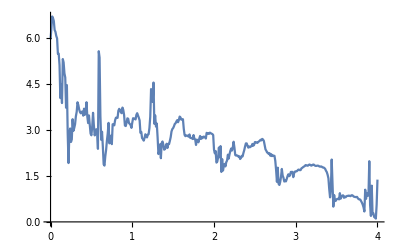

```mathematica
ListPlot[%115,Joined->True]
```

```mathematica
Mean[Table[tr10[0,0.001,1,0,01,100][[1,1]],1000]]
```

4.91838

```mathematica
Mean[Table[tr10[0,0.001,1,0,01,100][[1,1]],1500]]
```

4.9909

```mathematica
Mean[Table[tr10[0,0.001,1,0,01,100][[1,1]],2000]]
```

5.96152

```mathematica
Mean[Table[tr10[0,0.001,1,0,01,100][[1,1]],3500]]
```

5.93182

```mathematica
Mean[Table[tr10[0,0.001,1,0,01,100][[1,1]],1000]]
```

5.87052

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{gg=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
TT[t_]:=TT[t]=t*IdentityMatrix[7]
```

```mathematica
tr2[ω_,δ_,t_,ϵ_,ϵ1_,x_]:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],P=T[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]],gg}]},Inverse[IdentityMatrix[7]-c.ConjugateTranspose[P].J.P].c],x];J=J];Il1:=Inverse[IdentityMatrix[7]-sl1.TT[1].SR[ω,δ,1,0].TT[1]].sl1;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,1,0].TT[1].sl1.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];η]
```

```mathematica
Mean[Table[tr2[1,0.001,1,0,1,4],4000]]
```

4.42278

```mathematica
Timing[Mean[Table[tr3[1.5,0.001,1,0,1,10],6000]]]
```

{7.80679,3.1731}

```mathematica
Export["7sq100imp7.csv",Table[{ωean[Table[tr2[ω,0.001,1,0,0.7,100],1000]]},{ω,Range[0,4,0.01]}]]
```

7sq100imp7.csv

```mathematica
Import["7sq100imp7.csv"]
```

{{0.,1.0746},{0.01,1.13109},{0.02,1.09938},{0.03,1.10856},{0.04,1.10934},{0.05,1.07772},{0.06,1.13456},{0.07,1.16023},{0.08,1.22239},{0.09,1.37966},{0.1,1.53699},{0.11,1.87429},{0.12,2.22021},{0.13,2.92481},{0.14,4.24909},{0.15,8.31662},{0.16,9.81123},{0.17,7.69151},{0.18,5.81757},{0.19,4.2556},{0.2,2.87666},{0.21,2.16358},{0.22,1.67166},{0.23,1.20296},{0.24,1.11068},{0.25,1.04192},{0.26,1.10285},{0.27,1.15792},{0.28,1.22216},{0.29,1.28168},{0.3,1.28853},{0.31,1.35048},{0.32,1.41758},{0.33,1.44742},{0.34,1.42958},{0.35,1.46117},{0.36,1.50092},{0.37,1.469},{0.38,1.45827},{0.39,1.45526},{0.4,1.45675},{0.41,1.43642},{0.42,1.43819},{0.43,1.36417},{0.44,1.34107},{0.45,1.27128},{0.46,1.25366},{0.47,1.18503},{0.48,1.16292},{0.49,1.12117},{0.5,1.06891},{0.51,0.99445},{0.52,0.895232},{0.53,0.889778},{0.54,0.854661},{0.55,0.92703},{0.56,1.19355},{0.57,1.72603},{0.58,3.18545},{0.59,6.82193},{0.6,5.83509},{0.61,4.48792},{0.62,3.51706},{0.63,2.59177},{0.64,2.00404},{0.65,1.60172},{0.66,1.41291},{0.67,1.35519},{0.68,1.40095},{0.69,1.45011},{0.7,1.55057},{0.71,1.65833},{0.72,1.75215},{0.73,1.81427},{0.74,1.85509},{0.75,1.93704},{0.76,1.97471},{0.77,2.04515},{0.78,2.02002},{0.79,2.04089},{0.8,2.07074},{0.81,2.08899},{0.82,2.09482},{0.83,2.10992},{0.84,2.12919},{0.85,2.11312},{0.86,2.12521},{0.87,2.14112},{0.88,2.1527},{0.89,2.13016},{0.9,2.12106},{0.91,2.1371},{0.92,2.12003},{0.93,2.09892},{0.94,2.12157},{0.95,2.13377},{0.96,2.12012},{0.97,2.10436},{0.98,2.10813},{0.99,2.07155},{1.,2.07392},{1.01,2.0422},{1.02,2.01063},{1.03,1.99363},{1.04,1.99608},{1.05,1.91934},{1.06,1.91678},{1.07,1.90339},{1.08,1.83498},{1.09,1.82483},{1.1,1.72534},{1.11,1.72057},{1.12,1.65417},{1.13,1.61302},{1.14,1.52672},{1.15,1.43704},{1.16,1.35289},{1.17,1.22817},{1.18,1.12309},{1.19,0.956261},{1.2,0.869085},{1.21,0.821655},{1.22,1.04512},{1.23,2.05437},{1.24,4.9275},{1.25,3.78761},{1.26,3.13857},{1.27,2.50556},{1.28,1.98076},{1.29,1.73647},{1.3,1.49119},{1.31,1.35247},{1.32,1.2882},{1.33,1.43831},{1.34,1.48793},{1.35,1.6553},{1.36,1.76456},{1.37,1.82186},{1.38,1.90969},{1.39,1.95741},{1.4,1.97033},{1.41,2.01069},{1.42,2.0418},{1.43,2.04152},{1.44,2.07233},{1.45,2.08829},{1.46,2.11827},{1.47,2.0999},{1.48,2.11115},{1.49,2.14655},{1.5,2.12427},{1.51,2.135},{1.52,2.12669},{1.53,2.13943},{1.54,2.13691},{1.55,2.14828},{1.56,2.15774},{1.57,2.14828},{1.58,2.10639},{1.59,2.14294},{1.6,2.13183},{1.61,2.13794},{1.62,2.11737},{1.63,2.11659},{1.64,2.10778},{1.65,2.09518},{1.66,2.09723},{1.67,2.11564},{1.68,2.0981},{1.69,2.06597},{1.7,2.0646},{1.71,2.06943},{1.72,2.04441},{1.73,2.03445},{1.74,2.02323},{1.75,2.01391},{1.76,2.00375},{1.77,1.96643},{1.78,1.94935},{1.79,1.93624},{1.8,1.9293},{1.81,1.91027},{1.82,1.88903},{1.83,1.85544},{1.84,1.8636},{1.85,1.77402},{1.86,1.74702},{1.87,1.73776},{1.88,1.67852},{1.89,1.6692},{1.9,1.58624},{1.91,1.54191},{1.92,1.48367},{1.93,1.40546},{1.94,1.31678},{1.95,1.23396},{1.96,1.12088},{1.97,0.977417},{1.98,0.839604},{1.99,0.933648},{2.,2.65725},{2.01,3.39718},{2.02,2.7847},{2.03,2.42429},{2.04,2.10261},{2.05,1.75947},{2.06,1.59522},{2.07,1.31288},{2.08,1.21514},{2.09,1.20122},{2.1,1.22617},{2.11,1.30839},{2.12,1.36975},{2.13,1.48614},{2.14,1.56644},{2.15,1.58039},{2.16,1.64659},{2.17,1.693},{2.18,1.70515},{2.19,1.74133},{2.2,1.74732},{2.21,1.75853},{2.22,1.78203},{2.23,1.78985},{2.24,1.77886},{2.25,1.78699},{2.26,1.78531},{2.27,1.80106},{2.28,1.80371},{2.29,1.80217},{2.3,1.82183},{2.31,1.79763},{2.32,1.79802},{2.33,1.79961},{2.34,1.77482},{2.35,1.77924},{2.36,1.78042},{2.37,1.76943},{2.38,1.77299},{2.39,1.77122},{2.4,1.77812},{2.41,1.74621},{2.42,1.74827},{2.43,1.75792},{2.44,1.73416},{2.45,1.74301},{2.46,1.72931},{2.47,1.71132},{2.48,1.70333},{2.49,1.68668},{2.5,1.69086},{2.51,1.66436},{2.52,1.67831},{2.53,1.63137},{2.54,1.63406},{2.55,1.60713},{2.56,1.59656},{2.57,1.60983},{2.58,1.58711},{2.59,1.55206},{2.6,1.54891},{2.61,1.51373},{2.62,1.47803},{2.63,1.46998},{2.64,1.42735},{2.65,1.41051},{2.66,1.36814},{2.67,1.34872},{2.68,1.29266},{2.69,1.25071},{2.7,1.1825},{2.71,1.11273},{2.72,1.02672},{2.73,0.914516},{2.74,0.795889},{2.75,0.679671},{2.76,0.836308},{2.77,2.25703},{2.78,2.21206},{2.79,1.8436},{2.8,1.66829},{2.81,1.50652},{2.82,1.3234},{2.83,0.952542},{2.84,0.929316},{2.85,0.874535},{2.86,0.866725},{2.87,0.975732},{2.88,1.03943},{2.89,1.10218},{2.9,1.1495},{2.91,1.18424},{2.92,1.21609},{2.93,1.22624},{2.94,1.23518},{2.95,1.23508},{2.96,1.24237},{2.97,1.2427},{2.98,1.26475},{2.99,1.2406},{3.,1.24432},{3.01,1.2426},{3.02,1.24792},{3.03,1.25184},{3.04,1.24731},{3.05,1.25461},{3.06,1.24946},{3.07,1.24827},{3.08,1.22868},{3.09,1.23161},{3.1,1.21704},{3.11,1.21365},{3.12,1.21567},{3.13,1.21761},{3.14,1.20492},{3.15,1.20112},{3.16,1.19869},{3.17,1.17559},{3.18,1.15036},{3.19,1.1496},{3.2,1.13975},{3.21,1.141},{3.22,1.119},{3.23,1.1328},{3.24,1.09932},{3.25,1.08918},{3.26,1.06623},{3.27,1.06152},{3.28,1.0504},{3.29,1.02902},{3.3,1.01045},{3.31,0.980254},{3.32,0.961731},{3.33,0.927221},{3.34,0.892859},{3.35,0.840477},{3.36,0.817671},{3.37,0.768048},{3.38,0.714296},{3.39,0.659395},{3.4,0.571426},{3.41,0.616407},{3.42,1.37301},{3.43,1.21357},{3.44,1.17804},{3.45,1.04687},{3.46,0.92992},{3.47,0.768199},{3.48,0.601165},{3.49,0.541695},{3.5,0.486234},{3.51,0.469943},{3.52,0.499102},{3.53,0.549119},{3.54,0.576118},{3.55,0.60496},{3.56,0.607335},{3.57,0.626863},{3.58,0.628817},{3.59,0.627325},{3.6,0.622488},{3.61,0.633328},{3.62,0.637904},{3.63,0.618801},{3.64,0.617048},{3.65,0.621347},{3.66,0.620257},{3.67,0.597404},{3.68,0.606539},{3.69,0.591796},{3.7,0.584925},{3.71,0.569882},{3.72,0.564827},{3.73,0.55778},{3.74,0.534111},{3.75,0.545724},{3.76,0.526989},{3.77,0.49802},{3.78,0.47796},{3.79,0.461405},{3.8,0.440321},{3.81,0.430116},{3.82,0.37025},{3.83,0.332426},{3.84,0.286259},{3.85,0.544449},{3.86,0.544049},{3.87,0.553947},{3.88,0.386175},{3.89,0.645139},{3.9,0.417135},{3.91,0.334773},{3.92,0.159643},{3.93,0.0700096},{3.94,0.0496587},{3.95,0.0358469},{3.96,0.0108599},{3.97,0.0166772},{3.98,0.00546317},{3.99,0.00464817},{4.,0.00376791}}

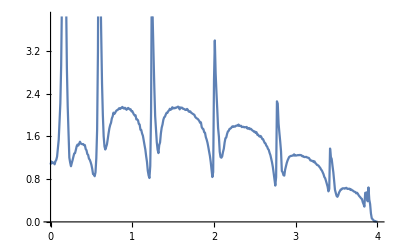

```mathematica
ListPlot[%73,Joined->True]
```

```mathematica
tr4[ω_,δ_,t_,ϵ_,ϵ1_,x_]:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],P=T[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]],gg}]},Inverse[IdentityMatrix[7]-c.ConjugateTranspose[P].J.P].c],x];J=J];Il1:=Inverse[IdentityMatrix[7]-sl1.TT[1].SR[ω,δ,1,0].TT[1]].sl1;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,1,0].TT[1].sl1.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];η]
```

```mathematica
Mean[Table[tr4[1,0.001,1,0,1,4],4000]]
```

4.25422

```mathematica
Export["7sq100imp66_7.csv",Table[{ωean[Table[tr4[ω,0.001,1,0,0.7,100],2000]]},{ω,Range[0,4,0.01]}]]
```

7sq100imp66_7.csv

```mathematica
Import["7sq100imp66_7.csv"]
```

{{0.,1.35778},{0.01,1.3566},{0.02,1.29484},{0.03,1.28425},{0.04,1.29423},{0.05,1.27207},{0.06,1.33538},{0.07,1.42437},{0.08,1.56062},{0.09,1.68577},{0.1,1.98704},{0.11,2.25836},{0.12,2.67942},{0.13,3.59402},{0.14,4.79399},{0.15,8.39225},{0.16,10.6249},{0.17,8.53237},{0.18,7.01303},{0.19,5.62321},{0.2,4.1399},{0.21,3.30701},{0.22,2.3615},{0.23,1.87394},{0.24,1.39467},{0.25,1.11357},{0.26,0.949569},{0.27,0.856639},{0.28,0.812231},{0.29,0.823391},{0.3,0.824239},{0.31,0.866574},{0.32,0.883883},{0.33,0.906229},{0.34,0.921432},{0.35,0.94705},{0.36,0.952371},{0.37,0.950363},{0.38,0.950922},{0.39,0.983578},{0.4,0.959288},{0.41,0.941293},{0.42,0.929001},{0.43,0.922428},{0.44,0.891645},{0.45,0.872843},{0.46,0.815065},{0.47,0.810133},{0.48,0.771762},{0.49,0.759407},{0.5,0.751981},{0.51,0.749415},{0.52,0.765062},{0.53,0.831984},{0.54,0.923229},{0.55,1.0655},{0.56,1.48478},{0.57,2.14343},{0.58,3.63401},{0.59,7.05584},{0.6,6.12474},{0.61,5.00497},{0.62,4.35321},{0.63,3.472},{0.64,2.83354},{0.65,2.0579},{0.66,1.66482},{0.67,1.22518},{0.68,1.08765},{0.69,1.05015},{0.7,1.05748},{0.71,1.14581},{0.72,1.20388},{0.73,1.29373},{0.74,1.33723},{0.75,1.42713},{0.76,1.47019},{0.77,1.52794},{0.78,1.56736},{0.79,1.59995},{0.8,1.63762},{0.81,1.65666},{0.82,1.67466},{0.83,1.68484},{0.84,1.71925},{0.85,1.69953},{0.86,1.70264},{0.87,1.71634},{0.88,1.72444},{0.89,1.72204},{0.9,1.72985},{0.91,1.71356},{0.92,1.71672},{0.93,1.72378},{0.94,1.71443},{0.95,1.73239},{0.96,1.69903},{0.97,1.705},{0.98,1.70378},{0.99,1.6824},{1.,1.66858},{1.01,1.65113},{1.02,1.63846},{1.03,1.61102},{1.04,1.58609},{1.05,1.53838},{1.06,1.52561},{1.07,1.48773},{1.08,1.45141},{1.09,1.41915},{1.1,1.3746},{1.11,1.3166},{1.12,1.26265},{1.13,1.21719},{1.14,1.14999},{1.15,1.05614},{1.16,0.964894},{1.17,0.894654},{1.18,0.839268},{1.19,0.755583},{1.2,0.761838},{1.21,0.833476},{1.22,1.15548},{1.23,2.30435},{1.24,4.6603},{1.25,4.18264},{1.26,3.64424},{1.27,3.12403},{1.28,2.56164},{1.29,1.98629},{1.3,1.62609},{1.31,1.32066},{1.32,1.09493},{1.33,1.03187},{1.34,1.07663},{1.35,1.15504},{1.36,1.23765},{1.37,1.37979},{1.38,1.47437},{1.39,1.53128},{1.4,1.6026},{1.41,1.66198},{1.42,1.71162},{1.43,1.72984},{1.44,1.76154},{1.45,1.77328},{1.46,1.79685},{1.47,1.81482},{1.48,1.82231},{1.49,1.82437},{1.5,1.85879},{1.51,1.84225},{1.52,1.83543},{1.53,1.85849},{1.54,1.86153},{1.55,1.83989},{1.56,1.85491},{1.57,1.84511},{1.58,1.8651},{1.59,1.85234},{1.6,1.84843},{1.61,1.84098},{1.62,1.84494},{1.63,1.84359},{1.64,1.85193},{1.65,1.82553},{1.66,1.82269},{1.67,1.8075},{1.68,1.81295},{1.69,1.82121},{1.7,1.80065},{1.71,1.78756},{1.72,1.76827},{1.73,1.78278},{1.74,1.73999},{1.75,1.74194},{1.76,1.7032},{1.77,1.70455},{1.78,1.708},{1.79,1.66931},{1.8,1.64773},{1.81,1.64296},{1.82,1.58848},{1.83,1.59273},{1.84,1.55623},{1.85,1.53477},{1.86,1.479},{1.87,1.4594},{1.88,1.42025},{1.89,1.36533},{1.9,1.32656},{1.91,1.24591},{1.92,1.21694},{1.93,1.12533},{1.94,1.02471},{1.95,0.955414},{1.96,0.854941},{1.97,0.745158},{1.98,0.742801},{1.99,0.930624},{2.,2.62255},{2.01,3.07646},{2.02,2.7184},{2.03,2.48302},{2.04,2.30112},{2.05,1.97498},{2.06,1.73344},{2.07,1.47135},{2.08,1.26107},{2.09,1.16495},{2.1,1.05553},{2.11,1.03539},{2.12,1.07157},{2.13,1.11173},{2.14,1.20487},{2.15,1.2909},{2.16,1.36018},{2.17,1.42793},{2.18,1.46624},{2.19,1.48998},{2.2,1.52775},{2.21,1.55473},{2.22,1.56534},{2.23,1.58312},{2.24,1.5904},{2.25,1.58707},{2.26,1.60376},{2.27,1.58897},{2.28,1.61443},{2.29,1.60567},{2.3,1.61985},{2.31,1.61265},{2.32,1.61438},{2.33,1.60828},{2.34,1.60202},{2.35,1.61737},{2.36,1.58546},{2.37,1.60043},{2.38,1.61047},{2.39,1.5972},{2.4,1.58413},{2.41,1.5888},{2.42,1.57232},{2.43,1.57378},{2.44,1.56677},{2.45,1.56766},{2.46,1.53955},{2.47,1.54341},{2.48,1.54015},{2.49,1.52457},{2.5,1.51306},{2.51,1.51476},{2.52,1.48688},{2.53,1.48412},{2.54,1.44528},{2.55,1.46006},{2.56,1.44008},{2.57,1.42304},{2.58,1.39713},{2.59,1.39009},{2.6,1.36751},{2.61,1.35697},{2.62,1.32493},{2.63,1.27559},{2.64,1.26933},{2.65,1.23073},{2.66,1.20581},{2.67,1.15696},{2.68,1.11331},{2.69,1.05736},{2.7,1.01137},{2.71,0.950033},{2.72,0.866296},{2.73,0.779119},{2.74,0.697851},{2.75,0.665978},{2.76,0.869957},{2.77,2.29086},{2.78,2.22232},{2.79,1.96185},{2.8,1.70567},{2.81,1.6199},{2.82,1.43446},{2.83,1.16871},{2.84,0.980275},{2.85,0.899483},{2.86,0.776269},{2.87,0.719079},{2.88,0.776893},{2.89,0.861411},{2.9,0.939462},{2.91,1.00361},{2.92,1.04178},{2.93,1.07046},{2.94,1.10817},{2.95,1.11636},{2.96,1.13623},{2.97,1.14341},{2.98,1.14972},{2.99,1.16716},{3.,1.157},{3.01,1.15472},{3.02,1.15564},{3.03,1.16188},{3.04,1.15684},{3.05,1.17214},{3.06,1.16355},{3.07,1.14808},{3.08,1.14598},{3.09,1.14969},{3.1,1.14015},{3.11,1.1383},{3.12,1.13761},{3.13,1.12799},{3.14,1.12349},{3.15,1.13453},{3.16,1.09031},{3.17,1.09728},{3.18,1.07617},{3.19,1.06824},{3.2,1.07179},{3.21,1.04986},{3.22,1.03446},{3.23,1.03191},{3.24,1.01792},{3.25,1.00572},{3.26,0.992898},{3.27,0.9716},{3.28,0.960983},{3.29,0.944373},{3.3,0.919321},{3.31,0.896147},{3.32,0.878625},{3.33,0.845618},{3.34,0.82313},{3.35,0.775096},{3.36,0.732294},{3.37,0.684555},{3.38,0.635772},{3.39,0.581386},{3.4,0.523653},{3.41,0.625139},{3.42,1.40537},{3.43,1.25119},{3.44,1.2296},{3.45,1.07371},{3.46,1.05046},{3.47,0.953613},{3.48,0.797808},{3.49,0.684349},{3.5,0.59353},{3.51,0.515087},{3.52,0.465318},{3.53,0.43403},{3.54,0.475095},{3.55,0.507592},{3.56,0.537091},{3.57,0.570458},{3.58,0.581215},{3.59,0.590374},{3.6,0.606548},{3.61,0.611001},{3.62,0.609152},{3.63,0.615073},{3.64,0.613971},{3.65,0.608774},{3.66,0.600201},{3.67,0.591069},{3.68,0.593966},{3.69,0.578108},{3.7,0.571331},{3.71,0.577242},{3.72,0.559909},{3.73,0.562683},{3.74,0.537739},{3.75,0.535038},{3.76,0.513698},{3.77,0.505242},{3.78,0.487374},{3.79,0.463284},{3.8,0.444637},{3.81,0.41592},{3.82,0.382802},{3.83,0.336051},{3.84,0.274438},{3.85,0.411768},{3.86,0.590955},{3.87,0.711328},{3.88,0.545495},{3.89,0.498876},{3.9,0.474329},{3.91,0.524969},{3.92,0.254869},{3.93,0.177938},{3.94,0.156351},{3.95,0.114842},{3.96,0.0320668},{3.97,0.0161279},{3.98,0.0117338},{3.99,0.00789292},{4.,0.00605221}}

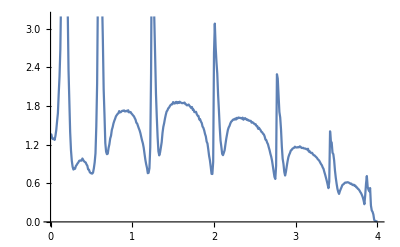

```mathematica
ListPlot[%75,Joined->True]
```

```mathematica
RandomChoice[Join[Table[RandomChoice[{h,i,f,e,d,c,b}],50],Table[a,100-50]],100]
```

{c,e,h,h,a,d,b,i,h,e,a,h,a,a,f,a,i,e,a,i,a,c,h,a,e,a,d,a,i,h,e,a,e,f,i,f,a,e,a,e,d,f,i,b,h,a,a,a,b,c,a,a,a,a,e,c,a,f,b,i,f,d,d,a,a,a,i,a,i,h,a,a,d,a,a,a,f,e,a,i,a,i,b,a,e,a,a,e,d,c,a,a,h,h,h,f,a,e,a,a}